# Passed Functions

```mathematica
ClearAll[$BaseSpacerSize, $BaseObjectSize, LevelSpacerFunction, LevelSpacerSize,LevelSizeFunction,LevelObjectSize, ColorElementsByLevel]
$BaseSpacerSize=1;
$BaseObjectSize=1;

LevelSpacerFunction[level_Integer,levelData_:{}]:=$BaseSpacerSize /level;
LevelSpacerSize[level_Integer, levelData_:{}, spacerFunction_:LevelSpacerFunction]:=spacerFunction[level, levelData];

LevelSizeFunction[level_Integer, levelData_:{}]:=$BaseObjectSize ;
LevelObjectSize[level_Integer, levelData_:{}, sizeFunction_:LevelSizeFunction]:=sizeFunction[level, levelData];

NumberOfElements[data_]:=1/;Not[ListQ[data]]
NumberOfElements[data_List]:=Total[Map[NumberOfElements,data]]


Options[ColorElementsByLevel]={"ColorGradient"->"DeepSeaColors"};
ColorElementsByLevel[data_List, opt:OptionsPattern[]]:=ColorElementsByLevel[data,Depth[data],0,opt]
ColorElementsByLevel[data_,max_, level_,opt: OptionsPattern[]]:=ColorData[OptionValue["ColorGradient"]][level/max]/;Not[ListQ[data]]

ColorElementsByLevel[data_List,max_, level_:1,opt:OptionsPattern[]]:=Map[ColorElementsByLevel[#,max,level+1,opt]&,data]
```

## Functioning version

```mathematica
ClearAll[SpacingOfElements, AggregateTo,LeftFirstTreeTraversalSpacing]

AggregateTo[list_,to_]:=list[[to]]/;to==1
AggregateTo[list_,to_]:=N[Total[list[[;;to-1]] ]+ list[[to]]]/;to>1

SpacingOfElements[element_, Level_:1,SpacingFunction_:LevelSpacerFunction,ObjectSize_:1]:=
ObjectSize+SpacingFunction[Level-1]/;Not[ListQ[element]]

SpacingOfElements[data_List,Level_:1,SpacingFunction_:LevelSpacerFunction,ObjectSize_:1]:=
Table[
SpacingOfElements[data[[i]],Level+1,SpacingFunction,ObjectSize]
+If[i==1,SpacingFunction[Level],0]
,
{i,Length[data]}]

LeftFirstTreeTraversalSpacing[data_]:=With[
{relativeSpacing=Flatten[SpacingOfElements[data]]},
Table[AggregateTo[relativeSpacing,i],{i,Length[relativeSpacing]}]
]

Options[ColorElementsByLevel]={"ColorGradient"->"DeepSeaColors"};
ColorElementsByLevel[data_List, opt:OptionsPattern[]]:=ColorElementsByLevel[data,Depth[data],0,opt]
ColorElementsByLevel[data_,max_, level_,opt: OptionsPattern[]]:=ColorData[OptionValue["ColorGradient"]][level/max]/;Not[ListQ[data]]

ColorElementsByLevel[data_List,max_, level_:1,opt:OptionsPattern[]]:=Map[ColorElementsByLevel[#,max,level+1,opt]&,data]
```

```mathematica
z[level_Integer,levelData_:{}]:=1
```

```mathematica
With[{fl=FoldList[Plus,Flatten[SpacingOfElements[data]]]},fl-First@fl]
```

```mathematica
{0,3/2,17/6,49/12,317/60,129/20,457/60,3679/420,4159/420,4649/420,1713/140,1881/140,2049/140,2217/140,598/35,1934/105,2074/105,738/35,1581/70,843/35,1791/70,5653/210,6073/210}
```

{0,3/2,17/6,49/12,317/60,129/20,457/60,3679/420,4159/420,4649/420,1713/140,1881/140,2049/140,2217/140,598/35,1934/105,2074/105,738/35,1581/70,843/35,1791/70,5653/210,6073/210}

{3,{2,3/2,{5/3,4/3},3/2},{2,{5/3,{3/2,5/4},4/3}},2}

{3,2,3/2,5/3,4/3,3/2,2,5/3,3/2,5/4,4/3,2}

{0,2.,3.5,5.16667,6.5,8.,10.,11.6667,13.1667,14.4167,15.75,17.75}

{2.,1.5,1.66667,1.33333,1.5,2.,1.66667,1.5,1.25,1.33333,2.}

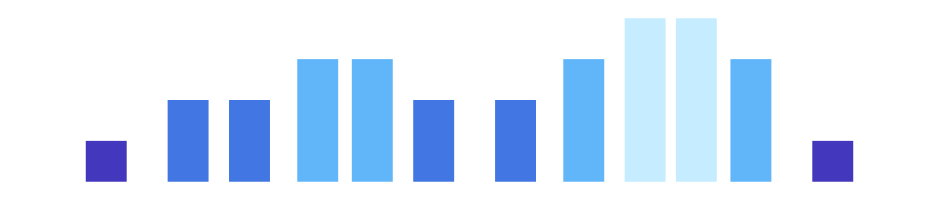

```mathematica
data={1,{2,2,{3,3},2},{2,{3,{4,4},3}},1};
(*s=SpacingOfElements[data,1,z]*)
s=SpacingOfElements[data]
fs=Flatten[s]
afs=Table[AggregateTo[fs,i],{i,Length[fs]}];
afs-=First@afs
(*lfs=With[{fl=FoldList[Plus,fs]},fl-First@fl];
afs==lfs*)
Differences@afs
colors=Flatten[ColorElementsByLevel[data,Depth[data]]];
graphicsData=Partition[Flatten[Riffle[Partition[Riffle[Flatten[data],afs],{2}],colors]],{3}];
Graphics@Join[
(*Table[{Blue,Rectangle[{afs[[i]],0},{afs[[i+1]],0.5}]},{i,(Length@afs)-1}]*)
{}
,
({#[[3]],Rectangle[{#[[2]],0},{#[[2]]+1,#[[1]]}]}&/@graphicsData)
]
```

```mathematica
Dendrogram[{1,{2,2,{3,3},2},{2,{3,{4,4},3}},1}]
```

Dendrogram::mlcntinft: The type of feature {1,{2,2,{3,3},2},{2,{3,{4,4},3}},…} cannot be interpreted. In general, datasets cannot contain nested structures. See \*ButtonBox["FeatureTypes",
BaseStyle->"Link",
ButtonData->"paclet:ref/FeatureTypes"] to learn about possible feature types.

Dendrogram[{1,{2,2,{3,3},2},{2,{3,{4,4},3}},1}]

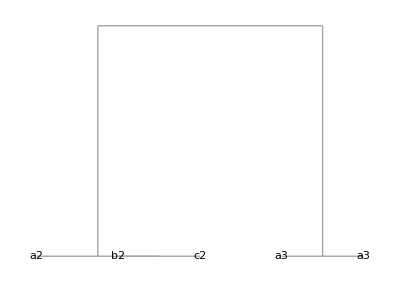

```mathematica
Dendrogram[{1-> a2,1->b2,b2->a3,b2->a3,1->c2}]
```

## Refractor

```mathematica
ClearAll[SpacingOfElements, AggregateTo,LeftFirstTreeTraversalSpacing]

AggregateTo[list_,to_]:=list[[to]]/;to==1
AggregateTo[list_,to_]:=N[Total[list[[;;to]] ]]/;to>1

Options[SpacingOfElements]={
SpacingFunction-> LevelSpacerFunction,
SizingFunction->LevelSizeFunction
};

SpacingOfElements[
element_, 
level_:1,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:= With[
{
spacer=OptionValue[SpacingFunction][level, element],
 size=OptionValue[SizingFunction][level, element]
},
size+spacer
]/;Not[ListQ[element]]


SpacingOfElements[
data_List,
level_:0,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:=With[
{last=Length[data]},
Table[
If[i==1,0,OptionValue[SpacingFunction][level+1, data[[i]]]]+
SpacingOfElements[data[[i]],level+1,i==1,i==last,opt],{i,last}]
]
```

{2,{5/2},{5/2},3}

{2,5/2,5/2,3}

{2,4.5,7.,10.}

{0,2.5,5.,8.}

{2.5,2.5,3.}

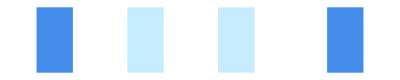

```mathematica
data={1,{1},{1},1};
s=SpacingOfElements[data]
fs=Flatten[s]
afs=Table[AggregateTo[fs,i],{i,Length[fs]}]
(*afs=Join[{0},afs][[;;-2]]*)
afs -= First[afs]
Differences@afs
colors=Flatten[ColorElementsByLevel[data,Depth[data]]];
graphicsData=Partition[Flatten[Riffle[Partition[Riffle[Flatten[data],afs],{2}],colors]],{3}];
Graphics@({#[[3]],Rectangle[{#[[2]],0},{#[[2]]+1,#[[1]]}]}&/@graphicsData)
```

```mathematica
LevelSizeFunction[4,{}]
```

1/4

## Refractor again

```mathematica
ClearAll[SpacingOfElements, AggregateTo,LeftFirstTreeTraversalSpacing]

AggregateTo[list_,to_]:=list[[to]]/;to==1
AggregateTo[list_,to_]:=N[Total[list[[;;to]] ]]/;to>1

Options[SpacingOfElements]={
SpacingFunction-> LevelSpacerFunction,
SizingFunction->LevelSizeFunction
};

Options[SizingOfElements]={
SpacingFunction-> LevelSpacerFunction,
SizingFunction->LevelSizeFunction
};


SpacingOfElements[
element_, 
level_:1,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:= With[
{
spacer=OptionValue[SpacingFunction][level, element]
},

If[firstQ&&!lastQ,0,spacer]
]/;Not[ListQ[element]]


SpacingOfElements[
data_List,
level_:0,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:=With[
{last=Length[data]},
Table[SpacingOfElements[data[[i]],level+1,i==1,i==last,opt],{i,last}]
]


SizingOfElements[
element_, 
level_:1,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:= With[
{
size=OptionValue[SizingFunction][level, element]
},
If[firstQ&&!lastQ,0,size]
]/;Not[ListQ[element]]


SizingOfElements[
data_List,
level_:0,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:=With[
{last=Length[data]},
Table[SizingOfElements[data[[i]],level+1,i==1,i==last,opt],{i,last}]
]
```

```mathematica
data={1,{1,1},1,1};
spoe=SpacingOfElements[data]
szoe=SizingOfElements[data]
fspoe=Flatten[SpacingOfElements[data]];
fszoe=Flatten[SizingOfElements[data]];
```

{0,{0,1/2},1,1}

{0,{0,1},1,1}

```mathematica
a=FoldList[Plus,fspoe]
b=FoldList[Plus,fszoe]
fl=a+b;
Differences@fl
```

{0,0,1/2,3/2,5/2}

{0,0,1,2,3}

{0,3/2,2,2}

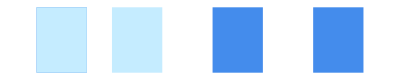

```mathematica
colors=Flatten[ColorElementsByLevel[data,Depth[data]]];
graphicsData=Partition[Flatten[Riffle[Partition[Riffle[Flatten[data],fl],{2}],colors]],{3}];
Graphics@({#[[3]],Rectangle[{#[[2]],0},{#[[2]]+1,#[[1]]}]}&/@graphicsData)
```

```mathematica
RectangleBox[_List,_List,_Rule]:>2
```

```mathematica
BarChart[{1}]//First//ReplacePart[#,Rectangle[_List,_List,_Rule]:>2,{1,-1}]&
```

{{Opacity[0],Rectangle[_List,_List,_Rule]:>2},{{},{Directive[EdgeForm[Directive[Thickness[Small],Opacity[0.693]]],RGBColor[0.982864, 0.7431472, 0.3262672]],{{Directive[EdgeForm[Directive[Thickness[Small],Opacity[0.693]]],RGBColor[0.982864, 0.7431472, 0.3262672]],}}},{},{}},{},{},{},{},{{Antialiasing→False,{Directive[Thickness[Tiny]],{Line[{{-1.27406,0.},{3.31051,0.}}]},{}},{{Directive[Thickness[Tiny]],Line[{{0.548798,0.},Offset[{-1.10218×10^-15,-6.},{0.548798,0.}]}],Line[{{1.4512,0.},Offset[{-1.10218×10^-15,-6.},{1.4512,0.}]}],{{},{},{}}},{}}}}}

```mathematica
ClearAll[SpacingOfElements, AggregateTo,LeftFirstTreeTraversalSpacing]

AggregateTo[list_,to_]:=list[[to]]/;to==1
AggregateTo[list_,to_]:=N[Total[list[[;;to]] ]]/;to>1

Options[SpacingOfElements]={
SpacingFunction-> LevelSpacerFunction,
SizingFunction->LevelSizeFunction
};

Options[SizingOfElements]={
SpacingFunction-> LevelSpacerFunction,
SizingFunction->LevelSizeFunction
};


SpacingOfElements[
element_, 
level_:1,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:= With[
{
spacer=OptionValue[SpacingFunction][level, element]
},

If[firstQ&&!lastQ,0,spacer]
]/;Not[ListQ[element]]


SpacingOfElements[
data_List,
level_:0,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:=With[
{last=Length[data]},
Table[SpacingOfElements[data[[i]],level+1,i==1,i==last,opt],{i,last}]
]


SizingOfElements[
element_, 
level_:1,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:= With[
{
size=OptionValue[SizingFunction][level, element]
},
If[firstQ&&!lastQ,0,size]
]/;Not[ListQ[element]]


SizingOfElements[
data_List,
level_:0,
firstQ_:False,
lastQ_:False,
opt: OptionsPattern[]
]:=With[
{last=Length[data]},
Table[SizingOfElements[data[[i]],level+1,i==1,i==last,opt],{i,last}]
]
```

## asrfarmfaer

```mathematica
d={q,w,{c,e},{x,g},h};
```

```mathematica
d
```

{q,w,{c,e},{x,g},h}